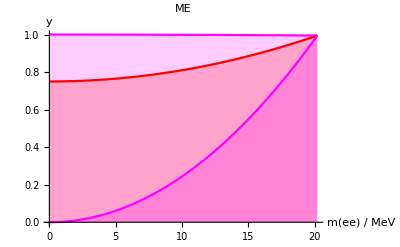

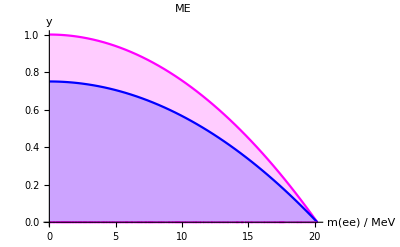

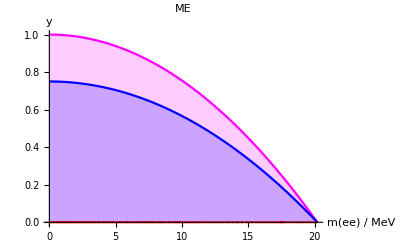

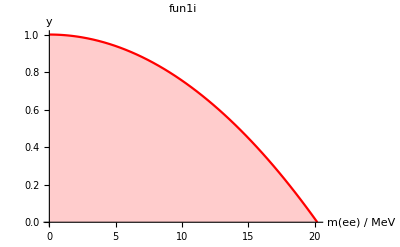

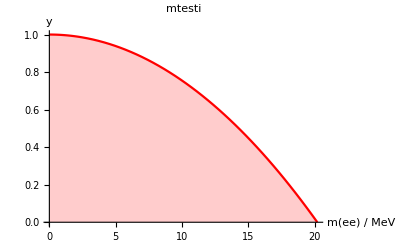

```mathematica
cs1=0.;
cs2=0.5;
cs3=1.;
n1=(m^2-m3^2)^2/16*2;
n2=(m^2-m3^2)^2*(1/6);
p3132[q_,cos_]:=2*p3p1[q,cos]*p3p2[q,cos]/n;
pall[q_,cos_]:=p3132[q,cos]-m3^2*q^2/2./n;
mtesti[q_]:=NIntegrate[mtest[q,c],{c,-1,1}];
Plot[{p3132[q,cs1],,  p3132[q,cs2],p3132[q,cs3]},                 {q,qmin,qmax},
PlotLabel->"ME",
FrameLabel->{"q/MeV","dM^2/dq"},
PlotRange->{{qmin,qmax},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"m(ee) / MeV",y},
PlotStyle->{Magenta,Blue,Red}]

Plot[{pall[q,cs1],pall[q,cs2],pall[q,cs3]}   ,                {q,qmin,qmax},
PlotLabel->"ME",
FrameLabel->{"q/MeV","dM^2/dq"},
PlotRange->{{qmin,qmax},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"m(ee) / MeV",y},
PlotStyle->{Magenta,Blue}
]
Plot[{mtest[q,cs1]/n,mtest[q,cs2]/n,mtest[q,cs3]/n},                   {q,qmin,qmax},
PlotLabel->"ME",
FrameLabel->{"q/MeV","dM^2/dq"},
PlotRange->{{qmin,qmax},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"m(ee) / MeV",y},
PlotStyle->{Magenta,Blue,Red}
]
Plot[{fun1i[q]}/n2,                   {q,qmin,qmax},
PlotLabel->"fun1i",
FrameLabel->{"q/MeV","dM^2/dq"},
PlotRange->{{qmin,qmax},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"m(ee) / MeV",y},
PlotStyle->{Magenta,Blue,Red}
]
Plot[{mtesti[q]}/n2,                   {q,qmin,qmax},
PlotLabel->"mtesti",
FrameLabel->{"q/MeV","dM^2/dq"},
PlotRange->{{qmin,qmax},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"m(ee) / MeV",y},
PlotStyle->{Magenta,Blue,Red}
]
```

```mathematica
mtesti[0.]
```

3.80365×10^9

```mathematica
Clear[m]
```

```mathematica
Clear[m3]
```

```mathematica
Simplify[mtest[q,c]]
```

0.125 ((1-1. c^2) m^4+(1-1. c^2) m3^4+(-2.+2. c^2) m3^2 q^2+(1-1. c^2) q^4+(-2.+2. c^2) m^2 (m3^2+q^2))

```mathematica
0.125 ((1-` c^2) m^4+(1-` c^2) m3^4+2(-1+` c^2) m3^2 q^2+(1-1 c^2) q^4+2(-1+` c^2) m^2 (m3^2+q^2))
```

0.125 ((1.-1. c^2) m^4+(1.-1. c^2) m3^4+(-2.+2. c^2) m3^2 q^2+(1.-1. c^2) q^4+(-2.+2. c^2) m^2 (m3^2+q^2))

```mathematica
Clear[m]
Clear[m3]
fun[q_,cos_]:=0.125((1-c^2) m^4+(1- c^2) m3^4+2(-1+ c^2) m3^2 q^2+(1-1 c^2) q^4+2(-1+c^2) m^2 (m3^2+q^2));
mel0[q_,cc_]:=0.125 (1-cc^2)(m^4+m3^4-2m3^2q^2+q^4-2m^2(m3^2+q^2));
mel0i[q_]:=Integrate[mel0[q,cc],{cc,-1,1}];
fun1i[q_]=fun1[q,0.]*4/3;
melo[q,c]
mel0i[q]
m=mhe4s;
m3=mhe4;
Plot[{fun1i[q]}/n2,                   {q,qmin,qmax},
PlotLabel->"fun1i",
FrameLabel->{"q/MeV","dM^2/dq"},
PlotRange->{{qmin,qmax},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"m(ee) / MeV",y},
PlotStyle->{Magenta,Blue,Red}
]
Plot[{mel0i[q]}/n2,                   {q,qmin,qmax},
PlotLabel->"fun1i",
FrameLabel->{"q/MeV","dM^2/dq"},
PlotRange->{{qmin,qmax},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"m(ee) / MeV",y},
PlotStyle->{Magenta,Blue,Red}
]
```

melo[q,0.]

0.166667 m^4-0.333333 m^2 m3^2+0.166667 m3^4-0.333333 m^2 q^2-0.333333 m3^2 q^2+0.166667 q^4

-Graphics-

-Graphics-

```mathematica
Simplify[mel0[q,cos]]
Simplify[mel0i[q/0.3333333333333333]]
```

0.125 (1-cos^2) (m^4+(m3^2-q^2)^2-2 m^2 (m3^2+q^2))

0.166667 m^4+0.166667 m3^4-3. m3^2 q^2+13.5 q^4+m^2 (-0.333333 m3^2-3. q^2)

```mathematica
fun[1,cos]-fun1[q,cos]
```

```mathematica
Simplify[0.125 (1-c^2+(1-c^2) m^4+2 (-1+c^2) m3^2+(1-c^2) m3^4+2 (-1+c^2) m^2 (1+m3^2))-0.125 (1-c^2) (2+m^4+m3^4-2 m3^2 q^2+q^4-2 m^2 (m3^2+q^4))]
```

-0.125-0.25 m3^2+0.25 m3^2 q^2-0.125 q^4+m^2 (-0.25+0.25 q^4)+c^2 (0.125+0.125 q^4+m3^2 (0.25-0.25 q^2)+m^2 (0.25-0.25 q^4))

0.

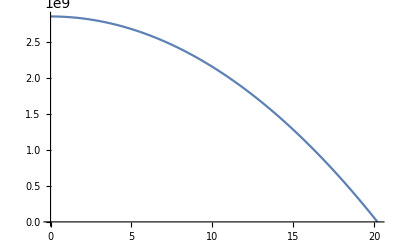

```mathematica
c=0.
m=mhe4s;
m3=mhe4;
Plot[0.125 ((1-1. c^2) m^4+(1-1. c^2) m3^4+(-2.+2. c^2) m3^2 q^2+(1-1. c^2) q^4+(-2.+2. c^2) m^2 (m3^2+q^2)),{q,0,qmax}]
```

```mathematica
Plot[fun1[q,c],{q,0,qmax}]
```

-Graphics-

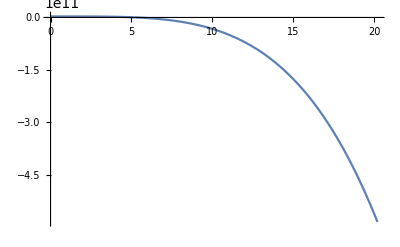

-Graphics-

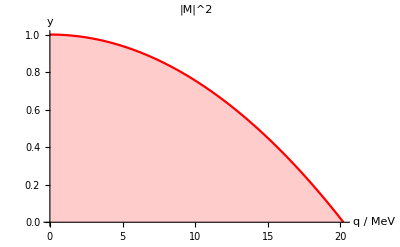

```mathematica
mtesti[q_]:=NIntegrate[mtest[q,c],{c,-1,1}];
m=mhe4s;
m3=mhe4;
mel[q_]:=(m^4+(m3^2-q^2)^2-2 m^2 (m3^2+q^2))/(m^2-m3^2)^2;
Plot[{mel[q]},                   {q,qmin,qmax},
PlotLabel->"|M|^2",
FrameLabel->{"q/MeV","dM^2/dq"},
PlotRange->{{qmin,qmax},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"q / MeV",y},
PlotStyle->{Magenta,Blue,Red}
]
```

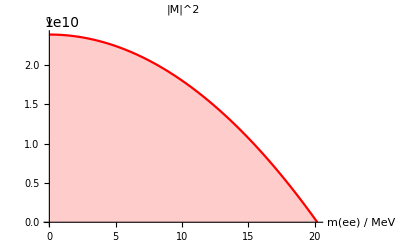

-Graphics-

```mathematica
Clear[m,m3]
```

```mathematica
m
```

m

```mathematica
m
```

```mathematica
Simplify[ p3p1[q,Cos[x]] ]
Simplify[ p3p2[q,Cos[x]] ]
Simplify[ p3p1[q,Cos[x]]*p3p2[q,Cos[x]]]
Simplify[ 2 p3p1[q,Cos[x]]*p3p2[q,Cos[x]]-m3^2*q^2/2]
Simplify[ 2 p3p1[0,Cos[x]]*p3p2[0,Cos[x]]-m3^2*0^2/2]
```

1/4 (m^2-m3^2-q^2+√((m^2-(m3-q)^2) (m^2-(m3+q)^2)) Cos[x])

1/4 (m^2-m3^2-q^2-√((m^2-(m3-q)^2) (m^2-(m3+q)^2)) Cos[x])

1/32 (m^4+m3^4+6 m3^2 q^2+q^4-2 m^2 (m3^2+q^2)-(m^4+(m3^2-q^2)^2-2 m^2 (m3^2+q^2)) Cos[2 x])

1/8 (m^4+(m3^2-q^2)^2-2 m^2 (m3^2+q^2)) Sin[x]^2

1/8 (m^2-m3^2)^2 Sin[x]^2

-Graphics-

-Graphics-

-Graphics-

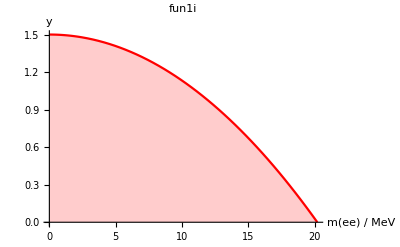

```mathematica
mtest[q_,cos_]:=2*p3p1[q,cos]*p3p2[q,cos]-m3^2*q^2/2. ;
mtesti[q_]:=NIntegrate[mtest[q,c],{c,-1,1}];

mel0[q_,cc_]:=0.125 (1-cc^2)(m^4+m3^4-2m3^2q^2+q^4-2m^2(m3^2+q^2));
mel0i[q_]:=Integrate[mel0[q,cc],{cc,-1,1}];

me1[q_,cos_]:=(2*( (m^2-m3^2-q^2)/4)^2-(m3*q)^2/2)-2*cos^2*(m*pq[q]/(2))^2;
mme1[q_]:=Integrate[me1[q,cc],{cc,-1,1}];




Plot[{mtesti[q]}/n2,                   {q,qmin,qmax},
PlotLabel->"fun1i",
FrameLabel->{"q/MeV","dM^2/dq"},
PlotRange->{{qmin,qmax},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"m(ee) / MeV",y},
PlotStyle->{Magenta,Blue,Red}
]
Plot[{mel0i[q]}/n2,                   {q,qmin,qmax},
PlotLabel->"meloi",
FrameLabel->{"q/MeV","dM^2/dq"},
PlotRange->{{qmin,qmax},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"m(ee) / MeV",y},
PlotStyle->{Magenta,Blue,Red}
]
Plot[{mme1[q]}/n2,                   {q,qmin,qmax},
PlotLabel->"fun1i",
FrameLabel->{"q/MeV","dM^2/dq"},
PlotRange->{{qmin,qmax},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"m(ee) / MeV",y},
PlotStyle->{Magenta,Blue,Red}
]
Plot[{me2[q]}/n2,                   {q,qmin,qmax},
PlotLabel->"fun1i",
FrameLabel->{"q/MeV","dM^2/dq"},
PlotRange->{{qmin,qmax},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"m(ee) / MeV",y},
PlotStyle->{Magenta,Blue,Red}
]
```

1.00084

0.

0.

5.69088×10^9

0.

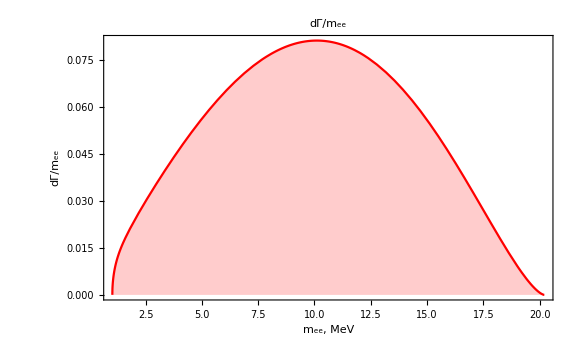

5.69088×10^9

20.1297

```mathematica
dgdq[q_]    :=me2[q]*phs[q]*norm;
NIntegrate[dgdq[qq],{qq,qmin,qmax}]
dgdq[qmin]
dgdq[qmin]
me2[qmin]
phs[qmin]
Plot[dgdq[q],                     {q,qmin,qmax},
PlotLabel->"dΓ/m_ee",
PlotRange->{{qmin,qmax},{0,All}},
Frame ->True, FrameLabel->{"m_ee, MeV","dΓ/m_ee"},
Filling->Axis,
PlotStyle->{Blue,Red},ImageSize->Large,LabelStyle->{ FontSize->20,Black}
]
me2[qmin]
p3[qmin]
```

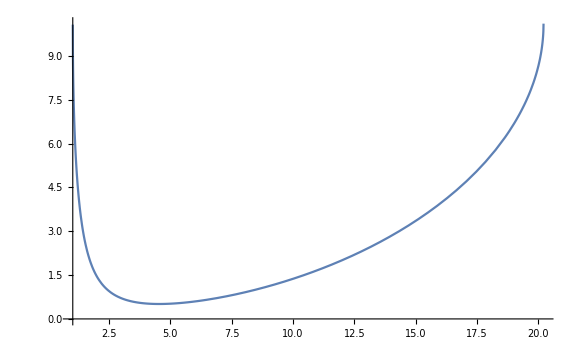

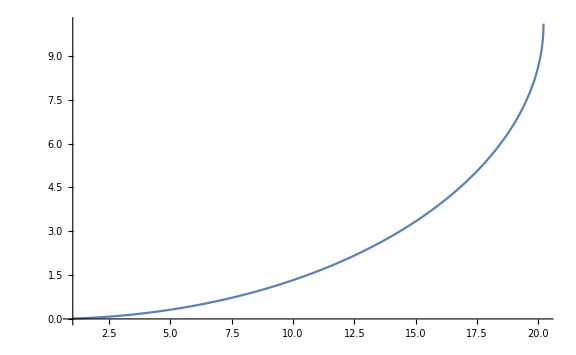

```mathematica
me=0.51099907;
Plot[e2[q,1.],{q,qmin,qmax}]
me=0.;
Plot[e2[q,1.],{q,qmin,qmax}]
```

```mathematica
n2=Integrate[dgdq_angle[qq,1.],{qq,qmin,qmax}];
```

```mathematica
n2
```

∫_1.022^20.21 dgdq_angle[qq,1.]ⅆqq

```mathematica
dgdqa[10,1]/10^7
dgdqa[10,0]/10^7
```

196.024

18767.6

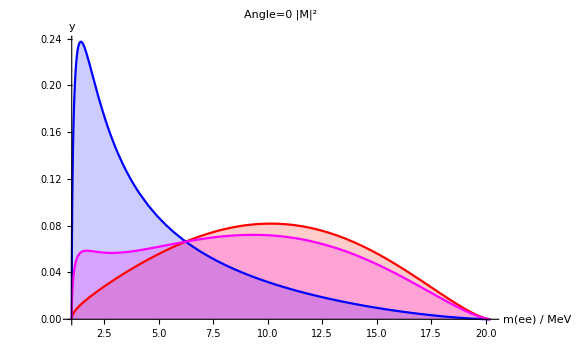

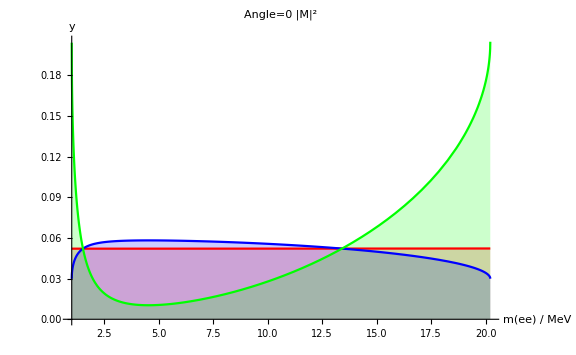

General::prng: Value of option PlotRange -> {{-1,1},{All}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

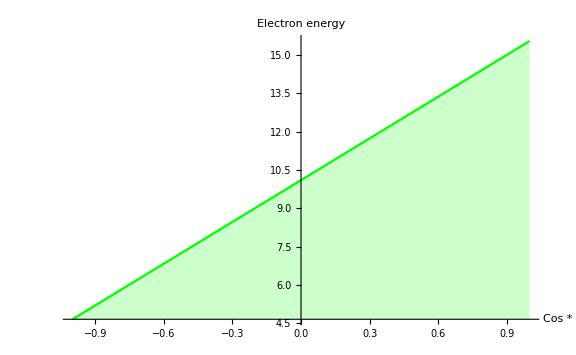

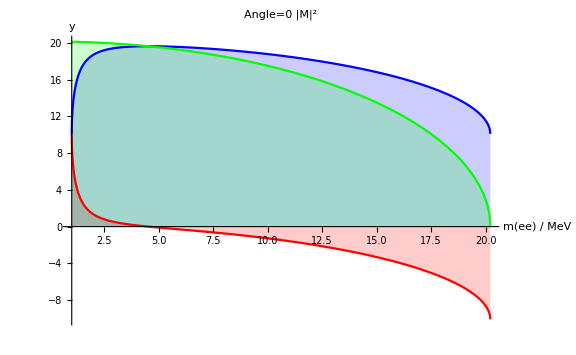

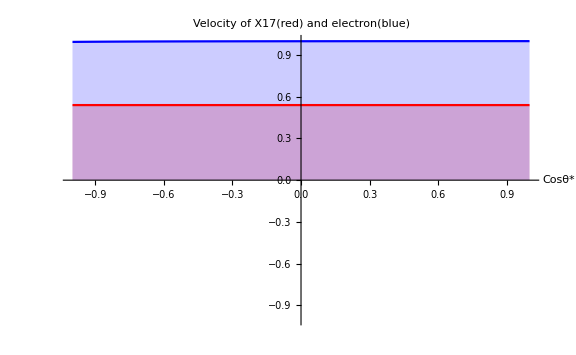

```mathematica
norm1=NIntegrate[dgdqa[qq,1.],{qq,qmin,qmax}];
norm0=NIntegrate[dgdqa[qq,0.],{qq,qmin,qmax}];
norm95=NIntegrate[dgdqa[qq,0.95],{qq,qmin,qmax}];

Plot[{dgdqa[q,0.]/norm0,dgdqa[q,1.]/norm1,dgdqa[q,0.95]/norm95},                  {q,qmin,qmax},
PlotLabel->"Angle=0 |M|^2",
FrameLabel->{"q/MeV","dM^2/dq"},
PlotRange->{{qmin,qmax},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"m(ee) / MeV",y},
PlotStyle->{Red,Blue,Magenta},ImageSize->Large,LabelStyle->{ FontSize->20,Black}
]
norm1=NIntegrate[e1[qq,1.],{qq,qmin,qmax}];
norm0=NIntegrate[e1[qq,0.],{qq,qmin,qmax}];
norm95=NIntegrate[e1[qq,-1.],{qq,qmin,qmax}];

Plot[{e1[q,0.0]/norm0,e1[q,1.0]/norm1,e1[q,-1.]/norm95},                  {q,qmin,qmax},
PlotLabel->"Angle=0 |M|^2",
FrameLabel->{"q/MeV","dM^2/dq"},
PlotRange->{{qmin,qmax},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"m(ee) / MeV",y},
PlotStyle->{Red,Blue,Green},ImageSize->Large,LabelStyle->{ FontSize->20,Black}
]
m17=17.;
cmin=-1;
cmax=1;
Plot[{e1[m17,cc]},                  {cc,cmin,cmax},
PlotLabel->"Electron energy",
FrameLabel->{"q/MeV","dM^2/dq"},
PlotRange->{{cmin,cmax},{All}},
Filling->Axis,
Axes->True,AxesLabel->{"Cos *"," "},
PlotStyle->{Red,Blue,Green},ImageSize->Large,LabelStyle->{ FontSize->20,Black}
]
Plot[{p1z[q,-1.],p2z[q,-1.],p3[q]},                  {q,qmin,qmax},
PlotLabel->"Angle=0 |M|^2",
FrameLabel->{"q/MeV","dM^2/dq"},
Filling->Axis,
Axes->True,AxesLabel->{"m(ee) / MeV",y},
PlotStyle->{Red,Blue,Green},ImageSize->Large,LabelStyle->{ FontSize->20,Black}
]
Plot[{vel[17.],p1[17.,cc]/e1[17.,cc]},                  {cc,-1,1},
PlotLabel->"Velocity of X17(red) and electron(blue)",
FrameLabel->{"q/MeV","dM^2/dq"},
Filling->Axis,
PlotRange->{{-1,1},{-1,1}},
Axes->True,AxesLabel->{"Cosθ*"," "},
PlotStyle->{Red,Blue,Green},ImageSize->Large,LabelStyle->{ FontSize->20,Black}
]
```